## Beach face (S_0<0 -> in salita)

```mathematica
g=9.81;
hl=6.0;
S0=-6.0/40.0;
t=-2 √(hl/g)S0
```

0.234619

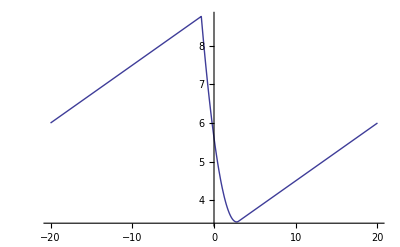

```mathematica
Clear[t,h0,δ,θ,h,m,xr,xl,c0]
δ=0;
θ=-ArcTan[6.0/40.0];
(*h0[x_]:=0/;x≤0
h0[x_]:=(x+20)*6.0/40.0/;x≥0*)
h0[x_]:=(x+20)*6.0/40.0
m=g(Cos[θ]Tan[δ]-Sin[θ]);
c0=√(g hl Cos[θ]);
xl[t_]:=2c0 t-1/2 m t^2
xr[t_]:=c0 t+1/2 m t^2
h[x_,t_]:=hl/;x≤-xr[t]
h[x_,t_]:=1/(9g Cos[θ])(2c0-x/t-(m t)/2)^2/;-xr[t]<x<xl[t]
h[x_,t_]:=0/;x≥xl[t]
Plot[h[x,0.2]+h0[x],{x,-20,20}]
```